### Bikin inset data w0 .33 m[r]

```mathematica
input1=ReadList[FileNameJoin[{NotebookDirectory[],"profil-v1_w0.33.dat"}],{Number,Number,Number,Number,Number}];
massamod=Transpose[input1][[3]];
rmod=Transpose[input1][[1]];
Dimensions[rmod][[1]]
```

1001

```mathematica
input2=ReadList[FileNameJoin[{NotebookDirectory[],"profil-vTOV_w0.33.dat"}],{Number,Number,Number,Number,Number}];
massaTOV=Transpose[input2][[3]];
rTOV=Transpose[input2][[1]];
Dimensions[rTOV][[1]]
```

1001

```mathematica
count=Dimensions[rmod][[1]];
```

```mathematica
datamod=Interpolation[Transpose[{rmod,massamod}]]
```

InterpolatingFunction[{{0.00002, 10.9345}}, <>]

```mathematica
dataTOV=Interpolation[Transpose[{rTOV,massaTOV}]]
```

InterpolatingFunction[{{0.00002, 10.9089}}, <>]

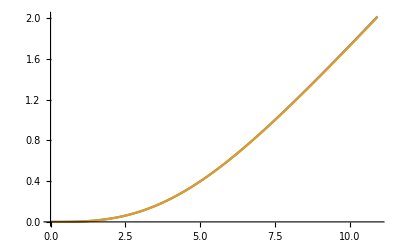

```mathematica
Plot[{datamod[x],dataTOV[x]},{x,rmod[[1]],rmod[[count]]}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"profil-v1_w0.33_inset.dat"}],Table[{x,dataTOV[x],datamod[x],100*Abs[(1-datamod[x]/dataTOV[x])]},{x,rmod[[1]],rmod[[count]],(rmod[[count]]-rmod[[1]])/1000}]]
```

InterpolatingFunction::dmval: Input value {10.9126} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {10.9236} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

C:\Users\ilham\Dropbox\00 SCGrav\ceknumerik\variasi2\plotprofil_varw\profil-v1_w0.33_inset.dat

### Bikin inset data w1 m[r]

```mathematica
input1=ReadList[FileNameJoin[{NotebookDirectory[],"profil-v1_w1.dat"}],{Number,Number,Number,Number,Number}];
massamod=Transpose[input1][[3]];
rmod=Transpose[input1][[1]];
Dimensions[rmod][[1]]
```

1001

```mathematica
input2=ReadList[FileNameJoin[{NotebookDirectory[],"profil-vTOV_w1.dat"}],{Number,Number,Number,Number,Number}];
massaTOV=Transpose[input2][[3]];
rTOV=Transpose[input2][[1]];
Dimensions[rTOV][[1]]
```

1001

```mathematica
count=Dimensions[rmod][[1]];
```

```mathematica
datamod=Interpolation[Transpose[{rmod,massamod}]]
```

InterpolatingFunction[{{0.00002, 14.1036}}, <>]

```mathematica
dataTOV=Interpolation[Transpose[{rTOV,massaTOV}]]
```

InterpolatingFunction[{{0.00002, 14.0744}}, <>]

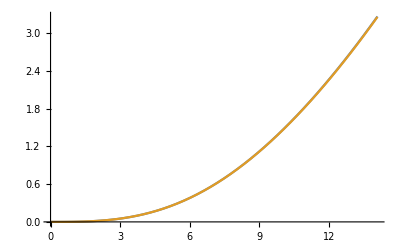

```mathematica
Plot[{datamod[x],dataTOV[x]},{x,rmod[[1]],rmod[[count]]}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"profil-v1_w1_inset.dat"}],Table[{x,dataTOV[x],datamod[x],100*Abs[(1-datamod[x]/dataTOV[x])]},{x,rmod[[1]],rmod[[count]],(rmod[[count]]-rmod[[1]])/1000}]]
```

InterpolatingFunction::dmval: Input value {14.0753} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {14.0894} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

C:\Users\ilham\Dropbox\00 SCGrav\ceknumerik\variasi2\plotprofil_varw\profil-v1_w1_inset.dat